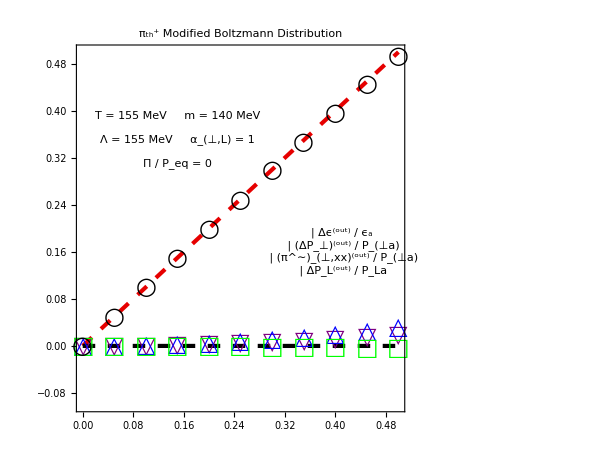

```mathematica
(*ANISOTROPIC PION BOLTZMANN GAS*)

T0 = 0.155;
mass = 0.140;  (* pion mass scale *)
sign = 0;
αT = 1.0;
αL = 1.0;
Λ = 0.155; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,0.000179133,0.00071662,0.00161272,0.00286788,0.00448269,0.00645796,0.00879465,0.0114939,0.0145571,0.0179856};

ΔPToverPTdata = {0.0,0.000314683,0.001259,0.00283379,0.00504047,0.00788103,0.011358,0.0154747,0.0202347,0.0256426,0.0317034};

ΔPLoverPLdata = {0.0,-3.53834*10^-05,-0.000141731,-0.000319633,-0.000570082,-0.000894473,-0.00129462,-0.00177276,-0.00233157,-0.0029742,-0.00370428};

piperpoverPTdata = {0.0,0.049993,0.099942,0.149812,0.199554,0.249127,0.298491,0.3476,0.396414,0.444886,0.492973};

style={Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{EdgeForm[Directive[Thick,Purple]],White,Polygon[{{1,Sqrt[3]},{0,0},{-1,Sqrt[3]}}]},ImageSize->16],Style["Δϵ^(out) / ϵ_a",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Blue]],White,Polygon[{{1,0},{0,Sqrt[3]},{-1,0}}]},ImageSize->16],Style["(ΔP_⊥)^(out) / P_(⊥a)",FontSize->14]},
{Graphics[{Directive[Thick,Black],Circle[]},ImageSize->16],Style["(π^∼)_(⊥,xx)^(out) / P_(⊥a)",FontSize->14]},{Graphics[{EdgeForm[Directive[Thick,Green]],White,Rectangle[]},ImageSize->16],Style["ΔP_L^(out) / P_La",FontSize->14]}}],Background->White];

legend2=Panel[Grid[{{Style["T = 155 MeV     m = 140 MeV",FontSize->14]},{},
{Style["Λ = 155 MeV     α_(⊥,L) = 1",FontSize->14]},{},{Style["Π / P_eq = 0",FontSize->14]}}],Background->White];


Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
piperpoverPTplot = Table[{frac[[i]],piperpoverPTdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.1,0.5},ImageSize->600,PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->22},AspectRatio->0.75],
ListPlot[{Δϵoverϵplot,ΔPToverPTplot,ΔPLoverPLplot,piperpoverPTplot},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{▽,24},{△,24},{□,24},{○,24}},PlotStyle->{Purple,Blue,Green,Black},BaseStyle->{FontSize->22},AspectRatio->0.75]}
},Epilog->{Inset[legend1,{0.41,0.16}],Inset[legend2,{0.15,0.35}]},ImageSize->{600,500},FrameLabel->{"(π^∼)_(⊥,xx)^(in) / P_(⊥a)"},PlotLabel->Style["π_th^+ Modified Boltzmann Distribution",FontSize->22]]
```